```mathematica
Clear["Global`*"]
```

## Efficiency factors, m_a,f_a in GeV

```mathematica
faMaPlane3evwPT30={{1,8181},{1.3,44323},{1.5,65725},{1.8,58076},{2,55909},{4,91016},{6,167220},{8,244103},{10,331492},{12,444057},{14,611733},{16,788218},{18,10^6},{20,1.3*10^6},{22,2.18*10^6},{22,2.47*10^6},{20,3*10^6},{18,3.4*10^6},{16,3.7*10^6},{14,3.9*10^6},{12,3.9*10^6},{10,3.78*10^6},{8,3.4*10^6},{6,2.84*10^6},{4,2*10^6},{2,783193},{1.8,651661},{1.5,598502},{1.3,340571},{1,164980}};

faMaPlane10evwPT30={{1,10232},{1.3,56618},{1.5,86419},{1.8,72533},{2,71082},{4,118362},{6,198543},{8,307219},{10,454181},{12,652662},{14,1.16*10^6},{14,1.54*10^6},{12,1.9*10^6},{10,2.1*10^6},{8,2.1*10^6},{6,1.9*10^6},{4,1.43*10^6},{2,541037},{1.8,453630},{1.5,413415},{1.3,198115},{1,112029}};


faMaPlane3evwHT100={{1,10880},{1.3,68957},{1.5,99307},{1.8,78132},{2,76631},{3,91054},{4,128554},(*{5,506851},*){6,211161},{8,328672},{10,505132},{12,740787},{13,1.16*10^6},{13,1.26*10^6},{12,1.5*10^6},{10,1.8*10^6},{8,1.8*10^6},(*{6.3,921178},{6.5,1.1*10^6},{6.3,1.2*10^6},*){6,1.67*10^6},(*{5,1.6*10^6},*){4,1.26*10^6},{3,941794},{2,474137},{1.8,391229},{1.5,360560},{1.3,155171},{1,100209}};

faMaPlane10evwHT100={(*{1,13023},*){1.8,137614},{2,107819},{3,130311},{4,172397},{5,239091},{6,306412},{7,459224},{7.5,601353},{7.5,679669},{7,780808},(*{6.3,921178},{6.5,1.1*10^6},{6.3,1.2*10^6},*){6,884514},{5,888240},{4,789501},{3,605536},{2,287247},{1.8,202213}(*,{1,74655}*)};
```

## Lifetime-M_a plot

```mathematica
WidthMaeV={{0.06101467495104318,0.001092360057946684},{0.07145879167371805,0.001886082856529087},{0.08288204433914359,0.003055275240744163},{0.09316297173802668,0.004915490999034501},{0.10115924860382464,0.007952302849178956},{0.10801320020308003,0.01358789367288134},{0.12108647825351149,0.030775608136111746},{0.1217211034015907,0.08795205984070696},{0.12210187849043819,0.06261246900447423},{0.12971738026738866,0.010305793554064345},{0.13120874936537485,0.0021486120173530086},{0.13139279065831777,0.0035134248920267817},{0.1366751796181479,0.0009914667752252367},{0.14710610932475887,0.0020526933785943394},{0.1528177356574717,0.00328809174269905},{0.16284481299712295,0.00542294792753641},{0.17541039092909116,0.008606539764508134},{0.1936875951937721,0.013579164685326993},{0.2131071247249957,0.020472834321932372},{0.2359536300558469,0.03076053228782612},{0.25994246065324067,0.04527984447601117},{0.28393129125063454,0.0658483716611192},{0.30906244711457087,0.09446965733614814},{0.3341936029785072,0.13584499241536585},{0.35932475884244364,0.19852851009132383},{0.38445591470637996,0.29080785056538955},{0.40730242003723116,0.4319187251126691},{0.42443729903536964,0.6635825113048992},{0.44042985276696545,1.0583112486799366},{0.4552800812320188,1.6733161407484718},{0.4689879844305296,2.701924946815279},{0.48269588762904025,4.462802831661535},{0.4918344897613808,7.113085326886795},{0.5009730918937213,11.337266013326168},{0.5091978338128277,20.500865189134114},{0.5158233203587747,32.46376583782562},{0.5203926214249449,54.05079646655601},{0.52267727195803,87.83185724971321},{0.5266373328820443,147.1849606889925},{0.5268404129294296,243.85780296033138},{0.5281350482315111,408.26711752199327},{0.5353697749196141,9461.616601558131},{0.5371467253342358,1332.940049023701},{0.5377813504823149,755.1868583818181},{0.5446353020815703,407.6102741665233},{0.5474276527331189,244.61770497154475},{0.5500930783550514,145.0956120568042},{0.5546623794212217,53.419598015815986},{0.5603740057539345,31.85559198401852},{0.5672279573531899,19.35345661066635},{0.5763665594855304,11.758250415228193},{0.587789812150956,7.284029782063863},{0.6026400406160092,4.6233801325980775},{0.6232018954137754,3.036228456689305},{0.6517600270773395,2.2101744527122476},{0.6871721103401588,2.035677212206167},{0.7225841936029783,2.2584618844850413},{0.7568539515992551,2.637848356572229},{0.791123709595532,3.088096612641593},{0.8196818412590962,4.172067173868072},{0.8368167202572344,6.586040298996421},{0.8482399729226601,10.772852912180529},{0.856236249788458,17.47858015103571},{0.864232526654256,28.82103190795785},{0.8710864782535114,45.78708070002618},{0.8779404298527668,79.12646288597118},{0.8847943814520222,130.68395644398743},{0.890506007784735,215.65808719928782},{0.8962176341174476,357.61655088612287},{0.9019292604501604,595.424170714163},{0.9064985615163307,983.3671207878889},{0.9110678625825009,1650.5658752337965},{0.9156371636486712,2748.1223411535143},{0.9179218141817563,4465.6638745793925},{0.9224911152479266,7617.82804713234},{0.9247757657810117,12631.824356595309},{0.9260450160771702,21576.477996478952},{0.9356913183279741,1.492075752410487*^6},{0.9369605686241326,193862.52037022123},{0.9378490438314432,58536.8746000322},{0.9383567439499066,102812.03192823388},{0.9497799966153323,25441.85779360961},{0.955618547977661,15381.839496936747},{0.9658994753765441,9380.758231692142},{0.9876036554408526,6380.367199523697},{1.023015738703672,6105.116133416894},{1.053858520900321,7735.792602949731},{1.0812743272973426,10895.106191927634},{1.1052631578947367,15854.93304973265},{1.1281096632255876,23512.076683809424},{1.1520984938229817,34961.86100976697},{1.1795143002200033,49013.216536455606},{1.2080724318835672,66294.21227473745},{1.2389152140802162,87015.65749205618},{1.2697579962768653,110448.87317263908},{1.3028854290065999,136045.61685623656},{1.336012861736334,165313.89407629013},{1.370282619732611,196007.35800745696},{1.404552377728888,228669.07655295098},{1.4399644609917073,258504.8745337518},{1.4753765442545266,282436.7004373795},{1.5119309527838887,296609.99364837306},{1.547343036046708,307110.96261202474},{1.58389744457607,317345.2586014868},{1.6193095278388894,317473.2573130415},{1.6558639363682515,317605.4391677541},{1.6924183448976136,306997.12546658015},{1.7278304281604329,285138.6877107935},{1.7632425114232522,257665.07666911042},{1.798654594686072,230695.43317421127},{1.8340666779488912,208106.38962724686},{1.8694787612117105,214418.11218182798},{1.9048908444745298,217312.17889303752},{1.9334489761380942,223175.0965222965}}
```

{{0.0610147,0.00109236},{0.0714588,0.00188608},{0.082882,0.00305528},{0.093163,0.00491549},{0.101159,0.0079523},{0.108013,0.0135879},{0.121086,0.0307756},{0.121721,0.0879521},{0.122102,0.0626125},{0.129717,0.0103058},{0.131209,0.00214861},{0.131393,0.00351342},{0.136675,0.000991467},{0.147106,0.00205269},{0.152818,0.00328809},{0.162845,0.00542295},{0.17541,0.00860654},{0.193688,0.0135792},{0.213107,0.0204728},{0.235954,0.0307605},{0.259942,0.0452798},{0.283931,0.0658484},{0.309062,0.0944697},{0.334194,0.135845},{0.359325,0.198529},{0.384456,0.290808},{0.407302,0.431919},{0.424437,0.663583},{0.44043,1.05831},{0.45528,1.67332},{0.468988,2.70192},{0.482696,4.4628},{0.491834,7.11309},{0.500973,11.3373},{0.509198,20.5009},{0.515823,32.4638},{0.520393,54.0508},{0.522677,87.8319},{0.526637,147.185},{0.52684,243.858},{0.528135,408.267},{0.53537,9461.62},{0.537147,1332.94},{0.537781,755.187},{0.544635,407.61},{0.547428,244.618},{0.550093,145.096},{0.554662,53.4196},{0.560374,31.8556},{0.567228,19.3535},{0.576367,11.7583},{0.58779,7.28403},{0.60264,4.62338},{0.623202,3.03623},{0.65176,2.21017},{0.687172,2.03568},{0.722584,2.25846},{0.756854,2.63785},{0.791124,3.0881},{0.819682,4.17207},{0.836817,6.58604},{0.84824,10.7729},{0.856236,17.4786},{0.864233,28.821},{0.871086,45.7871},{0.87794,79.1265},{0.884794,130.684},{0.890506,215.658},{0.896218,357.617},{0.901929,595.424},{0.906499,983.367},{0.911068,1650.57},{0.915637,2748.12},{0.917922,4465.66},{0.922491,7617.83},{0.924776,12631.8},{0.926045,21576.5},{0.935691,1.49208×10^6},{0.936961,193863.},{0.937849,58536.9},{0.938357,102812.},{0.94978,25441.9},{0.955619,15381.8},{0.965899,9380.76},{0.987604,6380.37},{1.02302,6105.12},{1.05386,7735.79},{1.08127,10895.1},{1.10526,15854.9},{1.12811,23512.1},{1.1521,34961.9},{1.17951,49013.2},{1.20807,66294.2},{1.23892,87015.7},{1.26976,110449.},{1.30289,136046.},{1.33601,165314.},{1.37028,196007.},{1.40455,228669.},{1.43996,258505.},{1.47538,282437.},{1.51193,296610.},{1.54734,307111.},{1.5839,317345.},{1.61931,317473.},{1.65586,317605.},{1.69242,306997.},{1.72783,285139.},{1.76324,257665.},{1.79865,230695.},{1.83407,208106.},{1.86948,214418.},{1.90489,217312.},{1.93345,223175.}}

#### Rescaling from eV to GeV units and from f_a=1/(32 Pi^2) TeV to f_a=1000 TeV

```mathematica
WidthMaGeV=Transpose@{WidthMaeV[[All,1]],WidthMaeV[[All,2]]/10^9*(1/(32 Pi^2*1000))^2};
WidthMaGeVFunc=Interpolation[WidthMaGeV,InterpolationOrder->1];
```

#### Calculation of lifetime using running α_s

```mathematica
mu=2.2/1000;
md=4.7/1000;
ms=20*md;
mc=1.275;
mb=4.18;
mt = 172.4;
mPi=135/1000;
mK=497/1000;
Mz=91.1876;
Mz=91.18;
GammaZ=2.495;
Mw=80.379;

GF=1.166 10^(-5);
ThetawatMz = ArcSin[Sqrt[0.231]];
v=Sqrt[1/(Sqrt[2]GF)];

g2atMz=2 Mz Cos[ThetawatMz]/v;
gpatMz = g2atMz Tan[ThetawatMz];
g1atMz=Sqrt[5/3]gpatMz;
alpha1atMz = g1atMz^2/4/Pi;
alpha2atMz = g2atMz^2/4/Pi;

b1=41/10;
b2=-19/6;

alpha1[μ_]:=1/(1/alpha1atMz-b1/(2Pi)Log[μ/Mz]);
alpha2[μ_]:=1/(1/alpha2atMz-b2/(2Pi)Log[μ/Mz]);
alphaEM[mu_]:=3/5alpha1[mu]alpha2[mu]/(alpha2[mu]+3/5alpha1[mu]);

LambdaQCD=0.48;
Nf[μ_]:=4(*using 4 quark flavors*)
beta0[μ_]=11-2/3Nf[μ];
beta1[μ_] = 102-38/3Nf[μ];
z[mu_]:=-beta0[mu]^2/E/beta1[mu](LambdaQCD^2/mu^2)^(beta0[mu]^2/beta1[mu]);

alphas[μ_]:=-4Pi beta0[μ]/beta1[μ]/ProductLog[-1,z[μ]];(* using the expression in 1604.08082v3 eq. 3.21 *)
```

```mathematica
nflav=3;
EA=(97/4-7/6nflav);
KggNNLO[ma_,c3_,fa_]:=1+alphas[ma]/Pi EA+(alphas[ma]/Pi)^2EA(3/4 EA+(51/8-19/24nflav)/(11/4-nflav/6));
KggNLO[ma_]:=1+alphas[ma]/Pi EA;
GammaaglugluNLO[ma_,c3_,fa_]:=1/(32Pi^3)alphas[ma]^2ma^3/fa^2c3^2KggNLO[ma];
GammaaglugluNNLO[ma_,c3_,fa_]:=1/(32Pi^3)alphas[ma]^2ma^3/fa^2c3^2KggNNLO[ma,c3,fa];
(*This is in GeV*)
LifetimeinmmNLO[ma_,c3_,fa_]:=1/GammaaglugluNLO[ma,c3,fa]*0.198*10^(-12);(*this is in mm*)
LifetimeinmmNNLO[ma_,c3_,fa_]:=1/GammaaglugluNNLO[ma,c3,fa]*0.198*10^(-12);(*this is in mm*)
```

```mathematica
Widthfunc[ma_]:=Piecewise[{{WidthMaGeVFunc[ma],ma<=1.82},{GammaaglugluNLO[ma,1,1000*1000],ma>1.82}}];
```

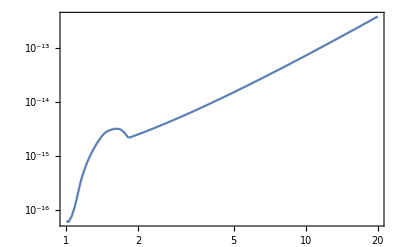

```mathematica
LogLogPlot[Widthfunc[ma],{ma,1,20},Frame->True]
```

#### Decay width into photons

```mathematica
c2=1;c1=1;
GammaPhoton[ma_,fa_]:=alphaEM[ma]^2/(256 Pi^3)ma^3/fa^2(c2+5/3 c1);
```

```mathematica
GeVtocm={{1/5.06*10^-21," ",{0.02,0},{}},{1/5.06*10^-20,"10^7",{0.02,0},{}},{1/5.06*10^-19," ",{0.02,0},{}},{1/5.06*10^-18," ",{0.02,0},{}},{1/5.06*10^-17,"10^4",{0.02,0},{}},{1/5.06*10^-16," ",{0.02,0},{}},{1/5.06*10^-15," ",{0.02,0},{}},{1/5.06*10^-14,"10",{0.02,0},{}},{1/5.06*10^-13," ",{0.02,0},{}},{1/5.06*10^-12," ",{0.02,0},{}},{1/5.06*10^-11,"10^-2",{0.02,0},{}}};
```

```mathematica
$CustomTicksPath = SetDirectory["C:\\Users\\novar\\Dropbox\\scripts\\math_nb\\CustomTicks"];
```

```mathematica
<<CustomTicks`
SetOptions[LogTicks,LogPlot->True,MajorTickLength->0.02,MinorTickLength->0.01];
SetOptions[LinTicks,MajorTickLength->0.02,MinorTickLength->0.01];
```

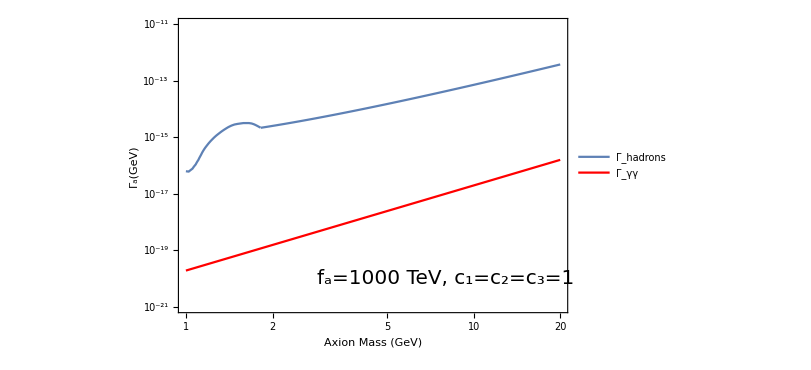

```mathematica
Show[LogLogPlot[Widthfunc[ma],{ma,1,20},PlotLegends->Placed[{Style["Γ_hadrons",FontSize->20,Black]},{0.85,0.3}],PlotRange-> {{1,20},{10^-21,10^-11}},Frame->True,Epilog->Style[Text[Style["f_a=1000 TeV, c_1=c_2=c_3=1",{20,Black}],{Log[8],Log[10^-20]}],20],FrameTicks->{{LogTicks[10,10^-21,10^-12,TickLabelStep->3,ShowMinorTicks-> False],GeVtocm},{LogTicks[10,0.9,20],LogTicks[10,0.9,20,ShowTickLabels-> False]}}],LogLogPlot[GammaPhoton[ma,1000*1000],{ma,1.0,20},PlotLegends->Placed[{Style["Γ_γγ",FontSize->20,Black]},{0.85,0.4}],PlotRange-> {{1,20},{10^-21,10^-11}},Frame->True,PlotStyle->Red],FrameLabel->{{Style["Γ_a(GeV)",FontSize->20,Black],Style["Lifetime (cm)",FontSize->20,Black]},{Style["Axion Mass (GeV)",FontSize->20,Black],None}},FrameTicksStyle->Directive[Black,18,AbsoluteThickness[1]],ImageSize-> 600]
```

```mathematica
GammaaglugluNLO[10,1,246]/KggNLO[10]
```

5.38766×10^-7

## B to K a searches

```mathematica
(*f[x_]:=x(1+x(Log[x]-1))/(1-x)^2;
gaW[fa_]:=alpha2 c2/(Pi fa);
gabs[fa_]=-3Sqrt[2]GF Mw^2(alpha2 c2/(Pi fa))/(16 Pi^2)(Vcb Conjugate[Vcs]f[mc^2/Mw^2]+Vtb Conjugate[Vts]f[mt^2/Mw^2]);*)
```

```mathematica
BtoKa={{0.05158633470429218,0.0000462698806786422},{0.054662705492485336,0.00004354230759022371},{0.05981682819103546,0.000039775828999793194},{0.06445361066093214,0.000036717370099428156},{0.06936047996715201,0.00003441986735287277},{0.07255681636867331,0.000032790687439206575},{0.08042680173394225,0.000029600663420411957},{0.08522308479728453,0.000028002292853042096},{0.09325873235326823,0.000025477626978018393},{0.10026170185282984,0.000023828723457568025},{0.10744421956855187,0.000022101649270378063},{0.12378744625184275,0.00001907899270675038},{0.1501521106695526,0.00001584811711798825},{0.1657704230606135,0.00001441085561921441},{0.17523276418502837,0.000013612594640478282},{0.19675610401968993,0.000012122542354179091},{0.20781987784987643,0.000011473954031255963},{0.23110388487901035,0.000010304855344261688},{0.24567517726112278,9.779861722780111*^-6},{0.26797603387275365,8.931509658116282*^-6},{0.2911277851879193,8.303173310322988*^-6},{0.3095334351375418,7.727558372255653*^-6},{0.3313876176030705,7.296703345411161*^-6},{0.3556993329498432,6.770251842085643*^-6},{0.3744935488984333,6.472150272383944*^-6},{0.4151135608659207,5.8832583538752985*^-6},{0.4436599788187467,5.51597666350928*^-6},{0.4813440747907938,5.069088502321296*^-6},{0.5851162888812775,4.248125280132725*^-6},{0.6209607564297349,3.99859654456169*^-6},{0.679927517506365,3.684385329792706*^-6},{0.7127881438052289,3.50922061796248*^-6},{0.7952033641799551,3.2606542271155387*^-6},{0.8453415984583258,3.040522529759324*^-6},{0.9770648035983731,2.7885408145577247*^-6},{1.0487455789763065,2.633474237630948*^-6},{1.1208654335076442,2.5333474503207404*^-6},{1.2239227667953883,2.4260756083483283*^-6},{1.272110920830231,2.381176717955988*^-6},{1.410092365317302,2.2881011072623935*^-6},{1.6885428127217708,2.218109318914291*^-6},{1.7550239366630365,2.217912645026188*^-6},{1.98331231322552,2.193450501093738*^-6},{2.0680434369211445,2.1952164108248557*^-6},{2.329539826977495,2.167763582727448*^-6},{2.4290624921257273,2.158462458390066*^-6},{2.7362083970772324,2.1333902005494332*^-6},{2.8531047681650015,2.1293455052210628*^-6},{3.234620720261005,2.0957516435129546*^-6},{3.3619738553941545,2.073035092095109*^-6},{3.7992895736929895,2.060044335458449*^-6},{3.9616029283156537,2.058609793859169*^-6},{4.462532863391636,2.22649606534058*^-6},{4.698321346931154,2.9140848896040047*^-6},{4.728657716436252,4.06349567938783*^-6},{4.759189963414764,5.672513846728813*^-6},{4.78991935261872,7.866514961154631*^-6}}
```

{{0.0515863,0.0000462699},{0.0546627,0.0000435423},{0.0598168,0.0000397758},{0.0644536,0.0000367174},{0.0693605,0.0000344199},{0.0725568,0.0000327907},{0.0804268,0.0000296007},{0.0852231,0.0000280023},{0.0932587,0.0000254776},{0.100262,0.0000238287},{0.107444,0.0000221016},{0.123787,0.000019079},{0.150152,0.0000158481},{0.16577,0.0000144109},{0.175233,0.0000136126},{0.196756,0.0000121225},{0.20782,0.000011474},{0.231104,0.0000103049},{0.245675,9.77986×10^-6},{0.267976,8.93151×10^-6},{0.291128,8.30317×10^-6},{0.309533,7.72756×10^-6},{0.331388,7.2967×10^-6},{0.355699,6.77025×10^-6},{0.374494,6.47215×10^-6},{0.415114,5.88326×10^-6},{0.44366,5.51598×10^-6},{0.481344,5.06909×10^-6},{0.585116,4.24813×10^-6},{0.620961,3.9986×10^-6},{0.679928,3.68439×10^-6},{0.712788,3.50922×10^-6},{0.795203,3.26065×10^-6},{0.845342,3.04052×10^-6},{0.977065,2.78854×10^-6},{1.04875,2.63347×10^-6},{1.12087,2.53335×10^-6},{1.22392,2.42608×10^-6},{1.27211,2.38118×10^-6},{1.41009,2.2881×10^-6},{1.68854,2.21811×10^-6},{1.75502,2.21791×10^-6},{1.98331,2.19345×10^-6},{2.06804,2.19522×10^-6},{2.32954,2.16776×10^-6},{2.42906,2.15846×10^-6},{2.73621,2.13339×10^-6},{2.8531,2.12935×10^-6},{3.23462,2.09575×10^-6},{3.36197,2.07304×10^-6},{3.79929,2.06004×10^-6},{3.9616,2.05861×10^-6},{4.46253,2.2265×10^-6},{4.69832,2.91408×10^-6},{4.72866,4.0635×10^-6},{4.75919,5.67251×10^-6},{4.78992,7.86651×10^-6}}

```mathematica
BtoKstara={{0.05158633470429218,0.00004544603920939483},{0.054662705492485336,0.000042767030927880705},{0.05981682819103546,0.00003942013157703594},{0.06445361066093214,0.00003606361237008151},{0.06936047996715201,0.00003320507847081209},{0.07255681636867331,0.00003163339760633473},{0.08042680173394225,0.00002855595989334454},{0.08522308479728453,0.000026772426902070095},{0.09325873235326823,0.000024578438794726256},{0.10026170185282984,0.000022782161456756473},{0.10744421956855187,0.000021321610302371436},{0.1157729038009574,0.000019879006022839102},{0.12378744625184275,0.00001824103977082405},{0.14049087208074776,0.00001617107524851884},{0.1501521106695526,0.00001515206484352913},{0.1657704230606135,0.00001377792813918769},{0.17523276418502837,0.000013014726932267044},{0.19675610401968993,0.00001159011802168372},{0.20781987784987643,0.000010970015819477494},{0.23110388487901035,9.941163538737963*^-6},{0.2688397827482396,8.592094038851095*^-6},{0.34651141064208285,6.558595022024045*^-6},{0.4164232058624899,5.577074838111545*^-6},{0.5909735357686339,4.032879461689522*^-6},{0.679927517506365,3.586423184247393*^-6},{0.7952033641799551,3.1739584406062584*^-6},{1.0487455789763065,2.633474237630948*^-6},{1.1208654335076442,2.5562064597399955*^-6},{1.2239227667953883,2.4260756083483283*^-6},{1.272110920830231,2.4243424626498173*^-6},{1.410092365317302,2.4365953088426106*^-6},{1.4989998631362134,2.4571945733164147*^-6},{1.8182618686983563,2.69490389287207*^-6},{1.9897049885537155,2.868854284664072*^-6},{2.170317967625756,3.093213452789764*^-6},{2.3597199393710855,3.39014736232974*^-6},{2.549191122888047,3.789057968415116*^-6},{2.796744029716555,4.533925478623145*^-6},{2.9369458904101005,5.036601616326229*^-6},{3.082191757727917,5.849504633491497*^-6},{3.224228285104317,6.944915524265424*^-6},{3.3619738553941545,8.263696771792402*^-6},{3.4607685663841075,9.871159539923772*^-6},{3.5624664513246667,0.000011961290459801613},{3.6671528226673016,0.000014501969306849821},{3.726635459424957,0.000017467059877565516},{3.8115355646851588,0.000021165868458823327},{3.8733601453466573,0.000025620089096571465},{3.9235410622701035,0.00003102897770147744},{3.9743720928748973,0.00003766262767406194},{4.0258616596416275,0.00004601746817104501}}
```

{{0.0515863,0.000045446},{0.0546627,0.000042767},{0.0598168,0.0000394201},{0.0644536,0.0000360636},{0.0693605,0.0000332051},{0.0725568,0.0000316334},{0.0804268,0.000028556},{0.0852231,0.0000267724},{0.0932587,0.0000245784},{0.100262,0.0000227822},{0.107444,0.0000213216},{0.115773,0.000019879},{0.123787,0.000018241},{0.140491,0.0000161711},{0.150152,0.0000151521},{0.16577,0.0000137779},{0.175233,0.0000130147},{0.196756,0.0000115901},{0.20782,0.00001097},{0.231104,9.94116×10^-6},{0.26884,8.59209×10^-6},{0.346511,6.5586×10^-6},{0.416423,5.57707×10^-6},{0.590974,4.03288×10^-6},{0.679928,3.58642×10^-6},{0.795203,3.17396×10^-6},{1.04875,2.63347×10^-6},{1.12087,2.55621×10^-6},{1.22392,2.42608×10^-6},{1.27211,2.42434×10^-6},{1.41009,2.4366×10^-6},{1.499,2.45719×10^-6},{1.81826,2.6949×10^-6},{1.9897,2.86885×10^-6},{2.17032,3.09321×10^-6},{2.35972,3.39015×10^-6},{2.54919,3.78906×10^-6},{2.79674,4.53393×10^-6},{2.93695,5.0366×10^-6},{3.08219,5.8495×10^-6},{3.22423,6.94492×10^-6},{3.36197,8.2637×10^-6},{3.46077,9.87116×10^-6},{3.56247,0.0000119613},{3.66715,0.000014502},{3.72664,0.0000174671},{3.81154,0.0000211659},{3.87336,0.0000256201},{3.92354,0.000031029},{3.97437,0.0000376626},{4.02586,0.0000460175}}

```mathematica
BtoKaFunc=Interpolation[BtoKa,InterpolationOrder->1];
BtoKstaraFunc=Interpolation[BtoKstara,InterpolationOrder->1];
```

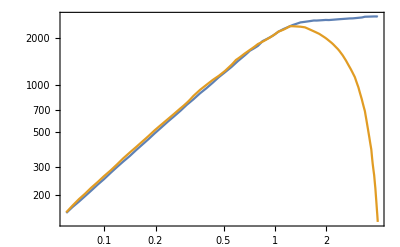

```mathematica
LogLogPlot[{alpha2[ma]/2/Pi/BtoKaFunc[ma],alpha2[ma]/2/Pi/BtoKstaraFunc[ma]},{ma,0.06,4.0},Frame->True]
```

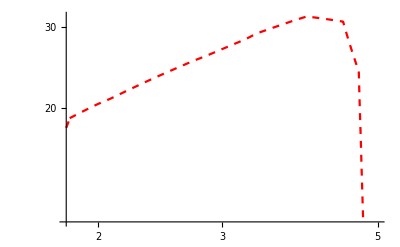

```mathematica
LogLogPlot[alpha2[ma]/2/Pi/BtoKaFunc[ma]Sqrt[GammaPhoton[ma,1000*1000]/Widthfunc[ma]],{ma,1.8,5},PlotStyle->{Dashed,Red}]
```

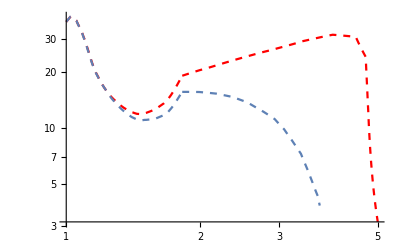

```mathematica
Show[LogLogPlot[alpha2[ma]/2/Pi/BtoKaFunc[ma]Sqrt[GammaPhoton[ma,1000*1000]/Widthfunc[ma]],{ma,1,5},PlotStyle->{Dashed,Red}],LogLogPlot[alpha2[ma]/2/Pi/BtoKstaraFunc[ma]Sqrt[GammaPhoton[ma,1000*1000]/Widthfunc[ma]],{ma,1,4},PlotStyle->Dashed]]
```

## BaBar Upsilon Bound

```mathematica
BaBarUpsilon={{2.0173577627772423,0.07225725956136636},{2.1909353905496625,0.06887476294004294},{2.4165863066538087,0.06565060727245506},{2.729026036644165,0.05893735839328112},{2.9199614271938277,0.05354857619900675},{3.0241080038572807,0.04983286699716787},{3.3018322082931526,0.0469341721682507},{3.5621986499517835,0.040646677715233004},{3.735776277724205,0.034782084318523386},{3.9440694310511093,0.02837035588659645},{4.239151398264224,0.023701981162494754},{4.586306653809065,0.021024768628211506},{4.88138862102218,0.018208204278211435},{5.037608486017358,0.016543385058636065},{5.332690453230472,0.013821152000738267},{5.6624879459980715,0.011546865526640904},{5.870781099324976,0.010617608598384556}};
BaBarUpsilon[[All,2]]=BaBarUpsilon[[All,2]]*1000/10/2;
```

## Belle II Upsilon projection

```mathematica
BelleIIUpsilon={{2.0810779461800184,0.19746692499291552},{2.3758477602299815,0.18330457550763873},{2.547526882698641,0.1763338711414358},{2.9103204999909025,0.15134109952113384},{3.187968676490083,0.1369663982288872},{3.3638125216062296,0.12761883557455553},{3.5063385855424754,0.11142768729419802},{3.7395630538017866,0.09594514354455994},{4.050529011480868,0.07730609094138777},{4.257839649933589,0.06751495545242178},{4.594719437419261,0.05903588947259657},{4.8227611397172545,0.05299583588226299},{5.009340714324703,0.048770954219740974},{5.216651352777424,0.042779412134357826},{5.41100507632685,0.038802638533851026},{5.566488055166391,0.0358741303244171},{5.864497097942177,0.03130345983210706},{6.134741323068045,0.028690998919428598},{6.320580502538164,0.0265390586045975},{6.56417050272011,0.02333857246082352},{6.797394970979422,0.020065998480780705},{6.926964120012373,0.018727377270656206},{6.978791779625553,0.016130667501268653}};
BelleIIUpsilon[[All,2]]=BelleIIUpsilon[[All,2]]*1000/10/2;
```

## LHCb diphoton search

```mathematica
LHCbdiphoton={{4.933461909353905,0.15375103712379873},{5.14175506268081,0.15748120842273952},{5.384763741562199,0.15748120842273952},{5.6624879459980715,0.15748120842273952},{5.974927675988428,0.15748120842273952},{6.217936354869817,0.15748120842273952}};
LHCbdiphoton[[All,2]]=LHCbdiphoton[[All,2]]*1000/10/2;
```

## LHCb diphoton projection

```mathematica
LHCbdiphotonProj={{2.0694310511089684,0.7391250149377016},{2.347155255544841,0.8233149127100045},{2.5380906460945036,0.8953717303712764},{2.8158148505303755,0.9854761473393395},{3.371263259402122,1.0977266251675522},{3.961427193828351,1.1725289678332336},{4.655737704918033,1.222762972858451},{5.384763741562199,1.2375068782625425},{6.217936354869817,1.2301128360427296},{6.634522661523626,1.222762972858451},{7.294117647058824,1.1938000547271632},{8.127290260366442,1.1725289678332336},{8.439729990356797,1.1795768811937692},{8.752169720347155,1.1866671586102053},{9.377049180327868,1.1655231654054645},{10.175506268081001,1.1311170633118146},{10.939247830279653,1.1043249117429634},{11.841851494696238,1.0717253746545934},{12.813886210221794,1.0400881719363673},{13.751205400192863,1.0093848955947156},{14.48023143683703,0.979587976236585},{15.209257473481195,0.9563850113219624},{15.972999035679845,0.9337316423536861},{16.979749276759883,0.9061679978303994},{17.743490838958532,0.8847040918102476},{18.57666345226615,0.8637485895990421},{19.548698167791706,0.8382508362818419}};
LHCbdiphotonProj[[All,2]]=LHCbdiphotonProj[[All,2]]*1000/10/2;
```

## LHC diphoton search

```mathematica
LHCdiphoton={{10.017743201159696,0.19241985712996282},{10.795521560319278,0.2241091861882455},{11.690088642152242,0.25354674781935266},{12.506704248804587,0.30400393135861375},{14.07587911978677,0.37797631496846157},{15.05957162107331,0.41538574400019845},{16.990983334523868,0.4307406098757766},{18.443991925548527,0.44022465045694864},{20.021210500090277,0.45319565996848266},{21.628096132285172,0.5053339022723001},{24.519047963074478,0.5928448512421322},{26.615523142036274,0.6282953163003716},{30.911531321633245,0.6468077383451735},{39.15992778678308,0.6658656200823736},{47.96176979303667,0.6515204520961788},{56.24418009111564,0.6515204520961795},{61.94586451314969,0.6237505994502803},{69.8863218122002,0.7811765700063218}};
LHCdiphoton[[All,2]]=LHCdiphoton[[All,2]]*1000/10/2;
```

```mathematica
LHCdiphoton
```

{{10.0177,9.62099},{10.7955,11.2055},{11.6901,12.6773},{12.5067,15.2002},{14.0759,18.8988},{15.0596,20.7693},{16.991,21.537},{18.444,22.0112},{20.0212,22.6598},{21.6281,25.2667},{24.519,29.6422},{26.6155,31.4148},{30.9115,32.3404},{39.1599,33.2933},{47.9618,32.576},{56.2442,32.576},{61.9459,31.1875},{69.8863,39.0588}}

## LHC diphoton projection

```mathematica
LHCdiphotonProj={{10.335748742611576,1.444111030124839},{10.41675194870266,1.655674907073349},{10.555218885200912,1.8887028412372682},{10.747260114954887,2.1677051287026514},{11.008658766187176,2.4895480928779996},{11.293217701000666,2.797604389944168},{11.630190195987225,3.1305641896662317},{12.030267736198718,3.461108602814217},{12.499210853652825,3.7952651762763225},{13.024755501324641,4.124997079517134},{13.572444151531206,4.434920474012405},{14.184885744448412,4.739430711704068},{14.824993404026184,5.032338904753966},{15.357572384143031,5.549372008451291},{15.909273777998852,6.131853171490679},{16.5294363962548,6.704943400621041},{17.17381540067919,7.275745111227719},{17.970104463286575,7.846675540137267},{18.813916346919882,8.406246067948292},{19.54751741285552,8.883278784310294},{20.489931854180114,9.31158723022065},{21.44616643062726,9.79714840866877},{22.44704311437383,10.284823283369438},{23.459965196174956,10.955667830355752},{24.518626688615736,11.623394524535593},{25.73879874518489,11.835824770162262},{26.98014527842239,11.78354154486186},{28.32311912370963,11.600027778909922},{29.689369443306564,11.227964820283665},{31.167016616534905,11.258282340293713},{32.66984166015921,11.556225391889786},{34.346224050253014,11.71591847613941},{36.05549379660809,11.902702699127484},{37.46114306840337,12.838257934130928},{39.15144081924623,13.825073466754061},{40.97872841174809,14.381257517162103},{42.95495482366519,14.445066731396242},{45.15934318283085,14.39399677055186},{47.3374553645589,14.1978003098433},{49.2575887841247,13.301101653051493},{51.482408358994526,12.48161551239784},{53.96462997548131,12.94722471669231},{56.23384024608581,13.914387283616392},{58.42600001376898,15.135444739729005},{60.79561886310297,14.398245695572287},{62.522272346687885,12.72129266020984},{64.20334224958565,11.268708710587989},{66.3165446005075,11.173868699799332},{69.10647709620505,11.305049607039726},{72.0128523203042,11.912287487592218},{75.48568139424025,11.984419850371626},{78.66031334252764,12.643405845209},{82.45375923072687,12.699504262976934},{86.17476874577028,13.387030466374956},{90.32947290133902,13.987379444098012},{94.4058528264888,14.768384804129353},{98.37557698702282,15.890763744498855},{102.66379950805539,16.79899353891182},{107.93246869509238,16.687805482889118},{112.30562456581731,17.92284571017845},{117.02910303252122,18.734144286627693},{122.85391816544352,18.665656623073726}};
LHCdiphotonProj[[All,2]]=LHCdiphotonProj[[All,2]]*1000/10/2;
```

# LHC Plot

## Paper coverage

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

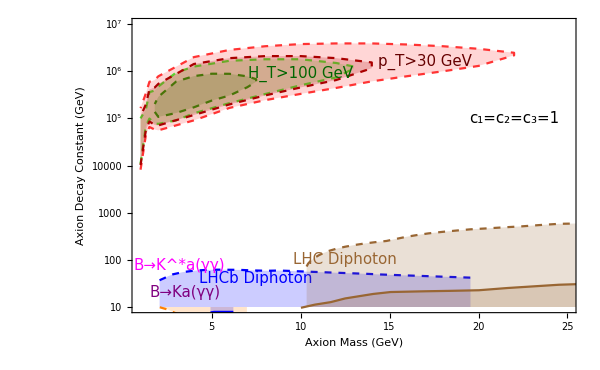

```mathematica
Show[LogPlot[alpha2[ma]/2/Pi/BtoKaFunc[ma]Sqrt[GammaPhoton[ma,1000*1000]/Widthfunc[ma]],{ma,1,5},PlotStyle->{Dashed,Purple},PlotRange->{{1,25},{10,10^7}},Filling->10,Frame->True,FrameTicks->{{LogTicks[10,10^-1,10^7,TickLabelStep->2],StripTickLabels[LogTicks[10,10^-1,10^7,TickLabelStep->2]]},{LinTicks[1,25],None}},BaseStyle->16,FrameTicksStyle->Directive[Black,16,AbsoluteThickness[1]]],LogPlot[alpha2[ma]/2/Pi/BtoKstaraFunc[ma]Sqrt[GammaPhoton[ma,1000*1000]/Widthfunc[ma]],{ma,1,4},PlotStyle->{Dashed,Magenta},Filling->10],ListLogPlot[BaBarUpsilon,PlotStyle->{Orange}],ListLogPlot[BelleIIUpsilon,PlotStyle->{Orange,Dashed},Joined->True,Filling->10],ListLogPlot[LHCbdiphoton,PlotStyle->{Blue},Joined->True,Filling->10],ListLogPlot[LHCbdiphotonProj,PlotStyle->{Blue,Dashed},Joined->True,Filling->10],ListLogPlot[LHCdiphoton,PlotStyle->{Brown},Joined->True,Filling->10],ListLogPlot[LHCdiphotonProj,PlotStyle->{Brown,Dashed},Joined->True,Filling->10],ListLogPlot[faMaPlane3evwHT100,Joined-> True,PlotStyle->{Dashed,Lighter[Green,0.2]},Filling->Bottom],
ListLogPlot[faMaPlane10evwHT100,Joined->True,PlotStyle->{Dashed,Darker[Green]},Filling->Bottom],
ListLogPlot[faMaPlane3evwPT30,Joined->True,PlotStyle->{Dashed,Lighter[Red,0.2]},Filling->Bottom],
ListLogPlot[faMaPlane10evwPT30,Joined->True,PlotStyle->{Dashed,Darker[Red]},Filling->Bottom],
FrameLabel->{{Style["Axion Decay Constant (GeV)",FontSize->16,Black],None},{Style["Axion Mass (GeV)",FontSize->16,Black],None}},ImageSize-> 600,Epilog->{Style[Text[Style["c_1=c_2=c_3=1",{15,Black}],{22,Log[1*10^5]}],20],Style[Text[Style["H_T>100 GeV",{15,Darker[Green,0.6]}],{10,Log[0.9*10^6]}],20],
Style[Text[Style["p_T>30 GeV",{15,Darker[Red,0.6]}],{17,Log[1.6*10^6]}],20],Style[Text[Style["LHCb Diphoton",{15,Blue}],{7.5,Log[4*10^1]}],20],Style[Text[Style["LHC Diphoton",{15,Brown}],{12.5,Log[1*10^2]}],20],Style[Text[Style["B→Ka(γγ)",{15,Purple}],{3.5,Log[2*10^1]}],20],
Style[Text[Style["B→K^*a(γγ)",{15,Magenta}],{3.2,Log[7.5*10^1]}],20]}]
```

```mathematica
faMaPlane3evwHT100PeVUnits=Transpose@{faMaPlane3evwHT100[[All,1]],faMaPlane3evwHT100[[All,2]]/10^6}
```

{{1,34/3125},{1.3,68957/1000000},{1.5,99307/1000000},{1.8,19533/250000},{2,76631/1000000},{3,45527/500000},{4,64277/500000},{6,211161/1000000},{8,10271/31250},{10,126283/250000},{12,740787/1000000},{13,1.16},{13,1.26},{12,1.5},{10,1.8},{8,1.8},{6,1.67},{4,1.26},{3,470897/500000},{2,474137/1000000},{1.8,391229/1000000},{1.5,4507/12500},{1.3,155171/1000000},{1,100209/1000000}}

```mathematica
faMaPlane10evwHT100PeVUnits=Transpose@{faMaPlane10evwHT100[[All,1]],faMaPlane10evwHT100[[All,2]]/10^6}
```

{{1.8,68807/500000},{2,107819/1000000},{3,130311/1000000},{4,172397/1000000},{5,239091/1000000},{6,76603/250000},{7,57403/125000},{7.5,601353/1000000},{7.5,679669/1000000},{7,97601/125000},{6,442257/500000},{5,11103/12500},{4,789501/1000000},{3,18923/31250},{2,287247/1000000},{1.8,202213/1000000}}

```mathematica
faMaPlane3evwPT30PeVUnits=Transpose@{faMaPlane3evwPT30[[All,1]],faMaPlane3evwPT30[[All,2]]/10^6}
```

{{1,8181/1000000},{1.3,44323/1000000},{1.5,2629/40000},{1.8,14519/250000},{2,55909/1000000},{4,11377/125000},{6,8361/50000},{8,244103/1000000},{10,82873/250000},{12,444057/1000000},{14,611733/1000000},{16,394109/500000},{18,1},{20,1.3},{22,2.18},{22,2.47},{20,3},{18,3.4},{16,3.7},{14,3.9},{12,3.9},{10,3.78},{8,3.4},{6,2.84},{4,2},{2,783193/1000000},{1.8,651661/1000000},{1.5,299251/500000},{1.3,340571/1000000},{1,8249/50000}}

```mathematica
faMaPlane10evwPT30PeVUnits=Transpose@{faMaPlane10evwPT30[[All,1]],faMaPlane10evwPT30[[All,2]]/10^6}
```

{{1,1279/125000},{1.3,28309/500000},{1.5,86419/1000000},{1.8,72533/1000000},{2,35541/500000},{4,59181/500000},{6,198543/1000000},{8,307219/1000000},{10,454181/1000000},{12,326331/500000},{14,1.16},{14,1.54},{12,1.9},{10,2.1},{8,2.1},{6,1.9},{4,1.43},{2,541037/1000000},{1.8,45363/100000},{1.5,82683/200000},{1.3,39623/200000},{1,112029/1000000}}

```mathematica
joined=Row[{Style["Axion Decay Constant",FontSize->16,Black],Style[" (PeV)",FontSize->16,Blue]}];
```

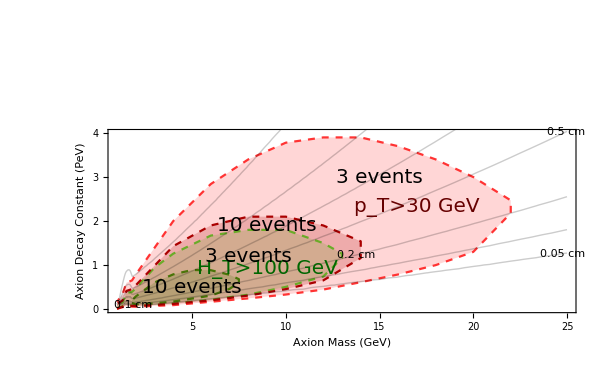

```mathematica
Show[ListPlot[faMaPlane3evwHT100PeVUnits,Joined-> True,PlotStyle->{Dashed,Lighter[Green,0.2]},Filling->Bottom,PlotRange->{{1,25},{0,4}}],ListPlot[faMaPlane10evwHT100PeVUnits,Joined->True,PlotStyle->{Dashed,Darker[Green]},Filling->Bottom],
ListPlot[faMaPlane3evwPT30PeVUnits,Joined-> True,PlotStyle->{Dashed,Lighter[Red,0.2]},Filling->Bottom],
ListPlot[faMaPlane10evwPT30PeVUnits,Joined->True,PlotStyle->{Dashed,Darker[Red]},Filling->Bottom],
ContourPlot[{1/(Widthfunc[ma]*(1/fa)^2*5*10^13)},{ma,1.83,25},{fa,0.1,7},ContourLabels->(Text[Framed[#3 "cm"],{#1,#2},Background->White]&),ContourShading->None,Contours->{0.05,0.1,0.2,0.5,1,2,5},ContourStyle-> Opacity[0.2]],
ContourPlot[{1/(Widthfunc[ma]*(1/fa)^2*5*10^13)},{ma,1,1.819},{fa,0.1,7},(*ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),*)ContourShading->None,Contours->{0.05,0.1,0.2,0.5,1,2,5},ContourStyle-> Opacity[0.2]],FrameLabel->{{joined,None},{Style["Axion Mass (GeV)",FontSize->16,Black],None}},ImageSize-> 600,Frame->True,FrameTicks->{{LinTicks[0,7],StripTickLabels[LinTicks[0,7]]},{LinTicks[1,25],None}},BaseStyle->16,FrameTicksStyle->Directive[Black,16,AbsoluteThickness[1]],Epilog->{(*Style[Text[Style["c_1=c_2=c_3=1",{18,Black}],{15,1*10^6}],20],*)Style[Text[Style["10 events",{20,Black}],{5,0.5}],20],
Style[Text[Style["H_T>100 GeV",{20,Darker[Green,0.6]}],{9,0.9}],20],Style[Text[Style["3 events",{20,Black}],{8,1.2}],20],Style[Text[Style["10 events",{20,Black}],{9,1.9}],20],Style[Text[Style["p_T>30 GeV",{20,Darker[Red,0.6]}],{17,2.3}],20],Style[Text[Style["3 events",{20,Black}],{15,3}],20]}]
```

## Theory plot

```mathematica
g3def=Sqrt[4 Pi 0.10792046236685181]; (* g3 at mtop *)
Mp=10^19;
mt=173;mb=4.2;mc=1.3;ms=0.095;md=0.0048;mu=0.0023;
v=174.1000;
x3Mp=-2(-7)*Log[Mp/mt]+16 π^2/g3def^2; (* RG evolve to the Planck Scale.  Assume that new particles at fa, have a mass larger than confinement scale so that they cancel out *)
yt=mt/v;yb=mb/v;yc=mc/v;ys=ms/v;yd=md/v;yu=mu/v;
(*Technically one should also run the yukawas simultaneously with QCDprime, but here we just use the weak scale values as an approximation, changing yt by order 1 does not change the final Subscript[Λ, QCD'] that much for example *)
mπ=0.1349766;
fπ=0.130;
mη=0.95778;
fη=0.95778; (* not 100% sure what value to use here *)
```

```mathematica
b0[Nf_]:=-11/3*3+2/3*Nf
```

```mathematica
x3[μ_,vs_]:=If[μ>yt vs,-2b0[6]*Log[μ/Mp]+x3Mp,If[μ>yb vs,-2 b0[5]*Log[μ/(yt vs)]-2b0[6]*Log[yt vs/Mp]+x3Mp,If[μ>yc vs,-2 b0[4]*Log[μ/(yb vs)]-2 b0[5]*Log[yb vs/(yt vs)]-2b0[6]*Log[yt vs/Mp]+x3Mp,If[μ>ys vs,-2 b0[3]*Log[μ/(yc vs)]-2 b0[4]*Log[yc vs/(yb vs)]-2 b0[5]*Log[yb vs/(yt vs)]-2b0[6]*Log[yt vs/Mp]+x3Mp,If[μ>yd vs,-2 b0[2]*Log[μ/(ys vs)]-2 b0[3]*Log[ys vs/(yc vs)]-2 b0[4]*Log[yc vs/(yb vs)]-2 b0[5]*Log[yb vs/(yt vs)]-2b0[6]*Log[yt vs/Mp]+x3Mp,If[μ>yu vs,-2 b0[1]*Log[μ/(yd vs)]-2 b0[2]*Log[yd vs/(ys vs)]-2 b0[3]*Log[ys vs/(yc vs)]-2 b0[4]*Log[yc vs/(yb vs)]-2 b0[5]*Log[yb vs/(yt vs)]-2b0[6]*Log[yt vs/Mp]+x3Mp,-2 b0[0]*Log[μ/(yu vs)]-2 b0[1]*Log[yu vs/(yd vs)]-2 b0[2]*Log[yd vs/(ys vs)]-2 b0[3]*Log[ys vs/(yc vs)]-2 b0[4]*Log[yc vs/(yb vs)]-2 b0[5]*Log[yb vs/(yt vs)]-2b0[6]*Log[yt vs/Mp]+x3Mp]]]]]]
```

```mathematica
ΛQCD=μ/.FindRoot[x3[μ,v]-1,{μ,1}]
vp=10^15;
Λmax=μ/.FindRoot[x3[μ,vp]-1,{μ,1}]
```

0.149896

4008.43

```mathematica
Expsummary={{10^-8,10^-8},{10^-5,10^-5},{0.9474635256553676,0.8933069785793951},{0.4572526698969273,0.8933069785793933},{0.25945527214039943,0.8933069785793933},{0.14722065648435284,0.8933069785793933},{0.08353625469578194,0.8933069785793933},{0.055730604012738404,0.8933069785793933},{0.03871601282054024,0.9441146805522602},{0.040315193628604064,1.7349581965943612},{0.031622776601683535,3.0166800781852783},{0.029163775740530962,4.695928194233292},{0.024804544143140934,7.725696865919662},{0.031622776601683535,14.19717474797677},{0.05139696800771513,36.358866572732175},{0.07104974114426788,78.87632589005145},{0.10649856353504203,191.13096700619198},{0.1596338544287929,489.4850877485863},{0.2206734069084572,1253.5679324035425},{0.3307739122991969,3585.9508304730716},{0.4216965034285788,7779.302629367969},{0.4216965034285822,12798.435465123512},{0.404969088912777,12798.435465123512},{0.27017217869999677,14295.68371155409},{0.2701721786999946,18336.356289907486},{0.281331751485873,29343.86008712665},{0.281331751485873,71105.24344104032},{0.281331751485873,145953.30710266155},{0.2491634725875976,192457.1543499105},{0.17309369546590408,253778.12257732335},{0.1064985635350429,353670.0830001766},{0.16622759633871387,649924.0209170739},{0.29295227500829235,1.2622659783166868*^6},{0.7136998820778977,4.0332522188211232*^6},{1.1139738599947933,8.278805770550614*^6},{2.0443105740506504,2.0060976911975503*^7},{3.190848980629082,4.117791856574968*^7},{4.98041606124833,8.452335022604518*^7},{8.42910085028456,1.9379254361887297*^8},{14.265824435249629,4.204103501127245*^8},{22.266720103519187,8.394091515005897*^8},{34.75486652866422,1.6759999448967204*^9},{61.2504628680027,4.2922242949140983*^9},{91.81013479068866,7.887632589005612*^9},{112.40386637720465,1.0400801138201468*^10}};
```

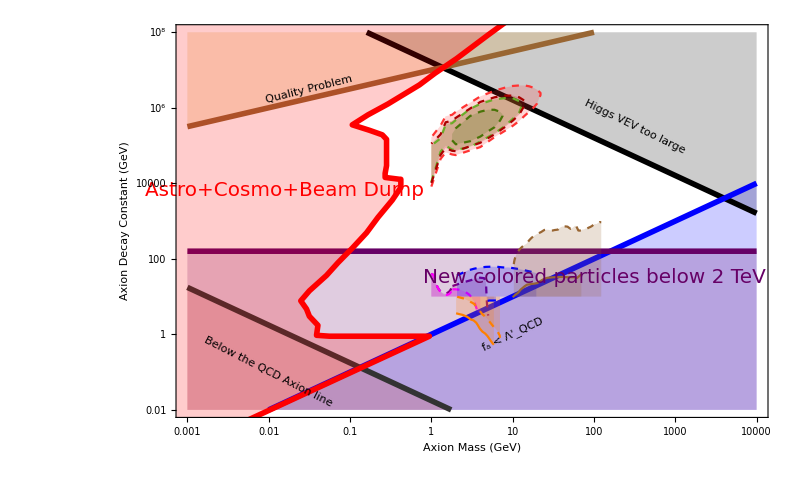

```mathematica
dim=6;
Show[LogLogPlot[{Λmax^2/ma,(ma^(2/(dim-2)) Mp^((dim-4)/(dim-2)))/10^(10/(dim-2)),ma,mπ fπ/ma,2000/(4π)},{ma,10^-3,10^4},Frame->True,Axes->False,ImageSize->400,PlotStyle->{{Black,Thickness[0.005]},{Brown,Thickness[0.005]},{Blue,Thickness[0.005]},{Darker[Gray,0.6],Thickness[0.005]},{Darker[Magenta,0.6],Thickness[0.005]}},Filling->{1->Top,2->Top,3->Bottom,4->Bottom,5->Bottom},FrameLabel->{Style["Axion Mass (GeV)",FontSize->20,Black],Style["Axion Decay Constant (GeV)",FontSize->20,Black]},Frame->True,PlotLabel->Style["",FontSize->20],BaseStyle->{FontSize->20},FrameStyle->Thickness[0.002],Epilog->{Style[Inset[Rotate[Text[Style["Higgs VEV too large",{20,Black}]],-26Degree],{Log[10^2.5],Log[10^5.5]}],20],Style[Inset[Rotate[Text[Style["Quality Problem",{20,Brown}]],14Degree],{Log[10^-1.5],Log[10^6.5]}],20],Style[Inset[Rotate[Text[Style["f_a < Λ'_QCD",{20,Blue}]],25Degree],{Log[10^1],Log[10^0]}],20],Style[Inset[Rotate[Text[Style["Below the QCD Axion line",{20,Darker[Gray,0.6]}]],-27Degree],{Log[10^-2],Log[10^-1]}],20],Style[Text[Style["New colored particles below 2 TeV",{20,Darker[Magenta,0.6]}],{Log[10^2],Log[10^1.5]}],20],Style[Text[Style["Astro+Cosmo+Beam Dump",{20,Red}],{Log[10^-1.8],Log[10^3.8]}],20](*,Style[Text[Style["Supernova + Star",{20,Black}],{Log[10^-4],Log[10^7]}],20]*)},PlotRange->{{10^-3,10^4},{10^-2,10^8}},FrameTicks->{{LogTicks[10,10^-5,10^13,TickLabelStep->4,ShowMinorTicks-> False],StripTickLabels[LogTicks[10,10^-5,10^13,TickLabelStep->4,ShowMinorTicks-> False]]},{LogTicks[10,10^-7,10^5,TickLabelStep->2,ShowMinorTicks-> False],None}},FrameTicksStyle->Directive[Black,20,AbsoluteThickness[1]]],(*Graphics[{EdgeForm[Thin],Directive[Opacity[0.3],Green],Rectangle[{Log[10^-9],Log[10^5]},{Log[10^-2],Log[10^8]}]}],Graphics[{EdgeForm[Thin],Directive[Opacity[0.3],Green],Rectangle[{Log[10^-9],Log[10^-5]},{Log[10^-4],Log[5 10^7]}]}],*)ListLogLogPlot[Expsummary,PlotRange->{{10^-8,Automatic},Automatic},PlotStyle->{Red,Thickness[0.005]},Joined->True,InterpolationOrder->1,Filling->Top],ListLogLogPlot[faMaPlane3evwHT100,Joined-> True,PlotStyle->{Dashed,Lighter[Green,0.2]},Filling->Bottom],
ListLogLogPlot[faMaPlane10evwHT100,Joined->True,PlotStyle->{Dashed,Darker[Green]},Filling->Bottom],
ListLogLogPlot[faMaPlane3evwPT30,Joined->True,PlotStyle->{Dashed,Lighter[Red,0.2]},Filling->Bottom],
ListLogLogPlot[faMaPlane10evwPT30,Joined->True,PlotStyle->{Dashed,Darker[Red]},Filling->Bottom],
LogLogPlot[alpha2[ma]/2/Pi/BtoKaFunc[ma]Sqrt[GammaPhoton[ma,1000*1000]/Widthfunc[ma]],{ma,1,5},PlotStyle->{Dashed,Purple},Filling->10],LogLogPlot[alpha2[ma]/2/Pi/BtoKstaraFunc[ma]Sqrt[GammaPhoton[ma,1000*1000]/Widthfunc[ma]],{ma,1,4},PlotStyle->{Dashed,Magenta},Filling->10],ListLogLogPlot[BaBarUpsilon,PlotStyle->{Orange},Joined->True,Filling->10],ListLogLogPlot[BelleIIUpsilon,PlotStyle->{Orange,Dashed},Joined->True,Filling->10],ListLogLogPlot[LHCbdiphoton,PlotStyle->{Blue},Joined->True,Filling->10],ListLogLogPlot[LHCbdiphotonProj,PlotStyle->{Blue,Dashed},Joined->True,Filling->10],ListLogLogPlot[LHCdiphoton,PlotStyle->{Brown},Joined->True,Filling->10],ListLogLogPlot[LHCdiphotonProj,PlotStyle->{Brown,Dashed},Joined->True,Filling->10],ImageSize->800]
```

## ZL redrawing

```mathematica
SetOptions[LogTicks,LogPlot->True,MajorTickLength->0.02,MinorTickLength->0.01];
SetOptions[LinTicks,MajorTickLength->0.02,MinorTickLength->0.01];
```

```mathematica
dim=6;
Rasterize[
Show[LogLogPlot[{Λmax^2/ma,(ma^(2/(dim-2)) Mp^((dim-4)/(dim-2)))/10^(10/(dim-2)),ma,mπ fπ/ma,2000/(4π),2000},{ma,10^-3,10^4},Frame->True,Axes->False,ImageSize->400,PlotStyle->{None,None,None,None,None,None},Filling->{1->{Top,Directive[Blue,Opacity[0.2]]},2->{Top,Directive[Blue,Opacity[0.2]]},3->{Bottom,Directive[Darker[Cyan],Opacity[0.2]]},5->{Bottom,Directive[Gray,Opacity[0.3]]},6->{Bottom,Directive[Gray,Opacity[0.15]]}},
FrameLabel->{Style["Axion Mass (GeV)",FontSize->20,Black],Style["Axion Decay Constant (GeV)",FontSize->20,Black]},Frame->True,PlotLabel->Style["",FontSize->20],BaseStyle->{FontSize->20},FrameStyle->Thickness[0.002],Epilog->{Style[Inset[Rotate[Text[Style["Quality Problem\n (from large Z2 Higgs VEV)",{20,Blue},TextAlignment->Center]],-32Degree],{Log[10^2.5],Log[10^5.5]}],20],Style[Inset[Rotate[Text[Style["Quality Problem",{20,Blue}]],14Degree],{Log[10^-1.5],Log[10^6.5]}],20],Style[Inset[Rotate[Text[Style["f_a < Λ'_QCD",{20,Darker[Cyan]}]],28Degree],{Log[10^3],Log[10^2.8]}],20],Style[Inset[Rotate[Text[Style["Below the QCD Axion line",{20,Darker[Gray,0.6]}]],-27Degree],{Log[10^-2],Log[10^-1]}],20],Style[Text[Style[" m_colored=f_a<2 TeV\n LHC direct searches for colored particles\n m_colored=4πf_a<2 TeV",{20,Darker[Gray,0.6]},TextAlignment->Left],{Log[10^-1],Log[10^2.4]}],20],
Style[Text[Style["Astro+Cosmo+Beam Dump",{20,Red}],{Log[10^-1.8],Log[10^3.8]}],20],
Style[Text[Style["Direct Axion searches\n(projected sensitivities)",{18,Magenta}],{Log[10^1],Log[10^1.8]}],20],
Style[Text[Style["Our Work",{20,Black}],{Log[10^1],Log[10^4.8]}],20](*,Style[Text[Style["Supernova + Star",{20,Black}],{Log[10^-4],Log[10^7]}],20]*)},PlotRange->{{10^-3,10^4},{10^1,10^8}},FrameTicks->{{LogTicks[10,10^-6,10^13,TickLabelStep->2,ShowMinorTicks-> True],StripTickLabels[LogTicks[10,10^-6,10^13,TickLabelStep->2,ShowMinorTicks-> True]]},{LogTicks[10,10^-7,10^5,TickLabelStep->1,ShowMinorTicks-> True],StripTickLabels[LogTicks[10,10^-7,10^5,TickLabelStep->1,ShowMinorTicks-> True]]}},FrameTicksStyle->Directive[Black,20,AbsoluteThickness[1]]],(*Graphics[{EdgeForm[Thin],Directive[Opacity[0.3],Green],Rectangle[{Log[10^-9],Log[10^5]},{Log[10^-2],Log[10^8]}]}],Graphics[{EdgeForm[Thin],Directive[Opacity[0.3],Green],Rectangle[{Log[10^-9],Log[10^-5]},{Log[10^-4],Log[5 10^7]}]}],*)ListLogLogPlot[Expsummary,PlotRange->{{10^-8,Automatic},Automatic},PlotStyle->{Red},Joined->True,InterpolationOrder->1,Filling->Top],ListLogLogPlot[faMaPlane3evwHT100,Joined-> True,PlotStyle->{Dashed,Lighter[Green,0.2]},Filling->Bottom],
ListLogLogPlot[faMaPlane10evwHT100,Joined->True,PlotStyle->{Dashed,Darker[Green]},Filling->Bottom],
ListLogLogPlot[faMaPlane3evwPT30,Joined->True,PlotStyle->{Dashed,Lighter[Red,0.2]},Filling->Bottom],
ListLogLogPlot[faMaPlane10evwPT30,Joined->True,PlotStyle->{Dashed,Darker[Red]},Filling->Bottom],
LogLogPlot[alpha2[ma]/2/Pi/BtoKaFunc[ma]Sqrt[GammaPhoton[ma,1000*1000]/Widthfunc[ma]],{ma,1,5},PlotStyle->{Dashed,Purple},Filling->10^-2],LogLogPlot[alpha2[ma]/2/Pi/BtoKstaraFunc[ma]Sqrt[GammaPhoton[ma,1000*1000]/Widthfunc[ma]],{ma,1,4},PlotStyle->{Dashed,Magenta},Filling->10^-2],ListLogLogPlot[BaBarUpsilon,PlotStyle->{Orange},Joined->True,Filling->10^-2],ListLogLogPlot[BelleIIUpsilon,PlotStyle->{Orange,Dashed},Joined->True,Filling->10^-2],ListLogLogPlot[LHCbdiphoton,PlotStyle->{Blue},Joined->True,Filling->10^-2],ListLogLogPlot[LHCbdiphotonProj,PlotStyle->{Blue,Dashed},Joined->True,Filling->10^-2],ListLogLogPlot[LHCdiphoton,PlotStyle->{Brown},Joined->True,Filling->10^-2],ListLogLogPlot[LHCdiphotonProj,PlotStyle->{Brown,Dashed},Joined->True,Filling->10^-2]
]
,ImageSize->800]
```

-Graphics-

# DUNE Plot

## DUNE coverage

## Paper coverage

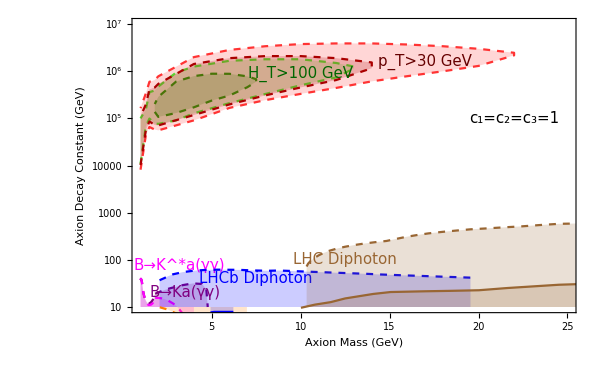

```mathematica
Show[LogPlot[alpha2[ma]/2/Pi/BtoKaFunc[ma]Sqrt[GammaPhoton[ma,1000*1000]/Widthfunc[ma]],{ma,1,5},PlotStyle->{Dashed,Purple},PlotRange->{{1,25},{10,10^7}},Filling->10,Frame->True,FrameTicks->{{LogTicks[10,10^-1,10^7,TickLabelStep->2],StripTickLabels[LogTicks[10,10^-1,10^7,TickLabelStep->2]]},{LinTicks[1,25],None}},BaseStyle->16,FrameTicksStyle->Directive[Black,16,AbsoluteThickness[1]]],LogPlot[alpha2[ma]/2/Pi/BtoKstaraFunc[ma]Sqrt[GammaPhoton[ma,1000*1000]/Widthfunc[ma]],{ma,1,4},PlotStyle->{Dashed,Magenta},Filling->10],ListLogPlot[BaBarUpsilon,PlotStyle->{Orange}],ListLogPlot[BelleIIUpsilon,PlotStyle->{Orange,Dashed},Joined->True,Filling->10],ListLogPlot[LHCbdiphoton,PlotStyle->{Blue},Joined->True,Filling->10],ListLogPlot[LHCbdiphotonProj,PlotStyle->{Blue,Dashed},Joined->True,Filling->10],ListLogPlot[LHCdiphoton,PlotStyle->{Brown},Joined->True,Filling->10],ListLogPlot[LHCdiphotonProj,PlotStyle->{Brown,Dashed},Joined->True,Filling->10],ListLogPlot[faMaPlane3evwHT100,Joined-> True,PlotStyle->{Dashed,Lighter[Green,0.2]},Filling->Bottom],
ListLogPlot[faMaPlane10evwHT100,Joined->True,PlotStyle->{Dashed,Darker[Green]},Filling->Bottom],
ListLogPlot[faMaPlane3evwPT30,Joined->True,PlotStyle->{Dashed,Lighter[Red,0.2]},Filling->Bottom],
ListLogPlot[faMaPlane10evwPT30,Joined->True,PlotStyle->{Dashed,Darker[Red]},Filling->Bottom],
FrameLabel->{{Style["Axion Decay Constant (GeV)",FontSize->16,Black],None},{Style["Axion Mass (GeV)",FontSize->16,Black],None}},ImageSize-> 600,Epilog->{Style[Text[Style["c_1=c_2=c_3=1",{15,Black}],{22,Log[1*10^5]}],20],Style[Text[Style["H_T>100 GeV",{15,Darker[Green,0.6]}],{10,Log[0.9*10^6]}],20],
Style[Text[Style["p_T>30 GeV",{15,Darker[Red,0.6]}],{17,Log[1.6*10^6]}],20],Style[Text[Style["LHCb Diphoton",{15,Blue}],{7.5,Log[4*10^1]}],20],Style[Text[Style["LHC Diphoton",{15,Brown}],{12.5,Log[1*10^2]}],20],Style[Text[Style["B→Ka(γγ)",{15,Purple}],{3.5,Log[2*10^1]}],20],
Style[Text[Style["B→K^*a(γγ)",{15,Magenta}],{3.2,Log[7.5*10^1]}],20]}]
```

```mathematica
faMaPlane3evwHT100PeVUnits=Transpose@{faMaPlane3evwHT100[[All,1]],faMaPlane3evwHT100[[All,2]]/10^6}
```

{{1,34/3125},{1.3,68957/1000000},{1.5,99307/1000000},{1.8,19533/250000},{2,76631/1000000},{3,45527/500000},{4,64277/500000},{6,211161/1000000},{8,10271/31250},{10,126283/250000},{12,740787/1000000},{13,1.16},{13,1.26},{12,1.5},{10,1.8},{8,1.8},{6,1.67},{4,1.26},{3,470897/500000},{2,474137/1000000},{1.8,391229/1000000},{1.5,4507/12500},{1.3,155171/1000000},{1,100209/1000000}}

```mathematica
faMaPlane10evwHT100PeVUnits=Transpose@{faMaPlane10evwHT100[[All,1]],faMaPlane10evwHT100[[All,2]]/10^6}
```

{{1.8,68807/500000},{2,107819/1000000},{3,130311/1000000},{4,172397/1000000},{5,239091/1000000},{6,76603/250000},{7,57403/125000},{7.5,601353/1000000},{7.5,679669/1000000},{7,97601/125000},{6,442257/500000},{5,11103/12500},{4,789501/1000000},{3,18923/31250},{2,287247/1000000},{1.8,202213/1000000}}

```mathematica
faMaPlane3evwPT30PeVUnits=Transpose@{faMaPlane3evwPT30[[All,1]],faMaPlane3evwPT30[[All,2]]/10^6}
```

{{1,8181/1000000},{1.3,44323/1000000},{1.5,2629/40000},{1.8,14519/250000},{2,55909/1000000},{4,11377/125000},{6,8361/50000},{8,244103/1000000},{10,82873/250000},{12,444057/1000000},{14,611733/1000000},{16,394109/500000},{18,1},{20,1.3},{22,2.18},{22,2.47},{20,3},{18,3.4},{16,3.7},{14,3.9},{12,3.9},{10,3.78},{8,3.4},{6,2.84},{4,2},{2,783193/1000000},{1.8,651661/1000000},{1.5,299251/500000},{1.3,340571/1000000},{1,8249/50000}}

```mathematica
faMaPlane10evwPT30PeVUnits=Transpose@{faMaPlane10evwPT30[[All,1]],faMaPlane10evwPT30[[All,2]]/10^6}
```

{{1,1279/125000},{1.3,28309/500000},{1.5,86419/1000000},{1.8,72533/1000000},{2,35541/500000},{4,59181/500000},{6,198543/1000000},{8,307219/1000000},{10,454181/1000000},{12,326331/500000},{14,1.16},{14,1.54},{12,1.9},{10,2.1},{8,2.1},{6,1.9},{4,1.43},{2,541037/1000000},{1.8,45363/100000},{1.5,82683/200000},{1.3,39623/200000},{1,112029/1000000}}

```mathematica
joined=Row[{Style["Axion Decay Constant",FontSize->16,Black],Style[" (PeV)",FontSize->16,Blue]}];
```

```mathematica
Show[ListPlot[faMaPlane3evwHT100PeVUnits,Joined-> True,PlotStyle->{Dashed,Lighter[Green,0.2]},Filling->Bottom,PlotRange->{{1,25},{0,4}}],ListPlot[faMaPlane10evwHT100PeVUnits,Joined->True,PlotStyle->{Dashed,Darker[Green]},Filling->Bottom],
ListPlot[faMaPlane3evwPT30PeVUnits,Joined-> True,PlotStyle->{Dashed,Lighter[Red,0.2]},Filling->Bottom],
ListPlot[faMaPlane10evwPT30PeVUnits,Joined->True,PlotStyle->{Dashed,Darker[Red]},Filling->Bottom],
ContourPlot[{1/(Widthfunc[ma]*(1/fa)^2*5*10^13)},{ma,1.83,25},{fa,0.1,7},ContourLabels->(Text[Framed[#3 "cm"],{#1,#2},Background->White]&),ContourShading->None,Contours->{0.05,0.1,0.2,0.5,1,2,5},ContourStyle-> Opacity[0.2]],
ContourPlot[{1/(Widthfunc[ma]*(1/fa)^2*5*10^13)},{ma,1,1.819},{fa,0.1,7},(*ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),*)ContourShading->None,Contours->{0.05,0.1,0.2,0.5,1,2,5},ContourStyle-> Opacity[0.2]],FrameLabel->{{joined,None},{Style["Axion Mass (GeV)",FontSize->16,Black],None}},ImageSize-> 600,Frame->True,FrameTicks->{{LinTicks[0,7],StripTickLabels[LinTicks[0,7]]},{LinTicks[1,25],None}},BaseStyle->16,FrameTicksStyle->Directive[Black,16,AbsoluteThickness[1]],Epilog->{(*Style[Text[Style["c_1=c_2=c_3=1",{18,Black}],{15,1*10^6}],20],*)Style[Text[Style["10 events",{20,Black}],{5,0.5}],20],
Style[Text[Style["H_T>100 GeV",{20,Darker[Green,0.6]}],{9,0.9}],20],Style[Text[Style["3 events",{20,Black}],{8,1.2}],20],Style[Text[Style["10 events",{20,Black}],{9,1.9}],20],Style[Text[Style["p_T>30 GeV",{20,Darker[Red,0.6]}],{17,2.3}],20],Style[Text[Style["3 events",{20,Black}],{15,3}],20]}]
```

-Graphics-

## Theory plot

```mathematica
g3def=Sqrt[4 Pi 0.10792046236685181]; (* g3 at mtop *)
Mp=10^19;
mt=173;mb=4.2;mc=1.3;ms=0.095;md=0.0048;mu=0.0023;
v=174.1000;
x3Mp=-2(-7)*Log[Mp/mt]+16 π^2/g3def^2; (* RG evolve to the Planck Scale.  Assume that new particles at fa, have a mass larger than confinement scale so that they cancel out *)
yt=mt/v;yb=mb/v;yc=mc/v;ys=ms/v;yd=md/v;yu=mu/v;
(*Technically one should also run the yukawas simultaneously with QCDprime, but here we just use the weak scale values as an approximation, changing yt by order 1 does not change the final Subscript[Λ, QCD'] that much for example *)
mπ=0.1349766;
fπ=0.130;
mη=0.95778;
fη=0.95778; (* not 100% sure what value to use here *)
```

```mathematica
b0[Nf_]:=-11/3*3+2/3*Nf
```

```mathematica
x3[μ_,vs_]:=If[μ>yt vs,-2b0[6]*Log[μ/Mp]+x3Mp,If[μ>yb vs,-2 b0[5]*Log[μ/(yt vs)]-2b0[6]*Log[yt vs/Mp]+x3Mp,If[μ>yc vs,-2 b0[4]*Log[μ/(yb vs)]-2 b0[5]*Log[yb vs/(yt vs)]-2b0[6]*Log[yt vs/Mp]+x3Mp,If[μ>ys vs,-2 b0[3]*Log[μ/(yc vs)]-2 b0[4]*Log[yc vs/(yb vs)]-2 b0[5]*Log[yb vs/(yt vs)]-2b0[6]*Log[yt vs/Mp]+x3Mp,If[μ>yd vs,-2 b0[2]*Log[μ/(ys vs)]-2 b0[3]*Log[ys vs/(yc vs)]-2 b0[4]*Log[yc vs/(yb vs)]-2 b0[5]*Log[yb vs/(yt vs)]-2b0[6]*Log[yt vs/Mp]+x3Mp,If[μ>yu vs,-2 b0[1]*Log[μ/(yd vs)]-2 b0[2]*Log[yd vs/(ys vs)]-2 b0[3]*Log[ys vs/(yc vs)]-2 b0[4]*Log[yc vs/(yb vs)]-2 b0[5]*Log[yb vs/(yt vs)]-2b0[6]*Log[yt vs/Mp]+x3Mp,-2 b0[0]*Log[μ/(yu vs)]-2 b0[1]*Log[yu vs/(yd vs)]-2 b0[2]*Log[yd vs/(ys vs)]-2 b0[3]*Log[ys vs/(yc vs)]-2 b0[4]*Log[yc vs/(yb vs)]-2 b0[5]*Log[yb vs/(yt vs)]-2b0[6]*Log[yt vs/Mp]+x3Mp]]]]]]
```

```mathematica
ΛQCD=μ/.FindRoot[x3[μ,v]-1,{μ,1}]
vp=10^15;
Λmax=μ/.FindRoot[x3[μ,vp]-1,{μ,1}]
```

0.149896

4008.43

```mathematica
Expsummary={{10^-8,10^-8},{10^-5,10^-5},{0.9474635256553676,0.8933069785793951},{0.4572526698969273,0.8933069785793933},{0.25945527214039943,0.8933069785793933},{0.14722065648435284,0.8933069785793933},{0.08353625469578194,0.8933069785793933},{0.055730604012738404,0.8933069785793933},{0.03871601282054024,0.9441146805522602},{0.040315193628604064,1.7349581965943612},{0.031622776601683535,3.0166800781852783},{0.029163775740530962,4.695928194233292},{0.024804544143140934,7.725696865919662},{0.031622776601683535,14.19717474797677},{0.05139696800771513,36.358866572732175},{0.07104974114426788,78.87632589005145},{0.10649856353504203,191.13096700619198},{0.1596338544287929,489.4850877485863},{0.2206734069084572,1253.5679324035425},{0.3307739122991969,3585.9508304730716},{0.4216965034285788,7779.302629367969},{0.4216965034285822,12798.435465123512},{0.404969088912777,12798.435465123512},{0.27017217869999677,14295.68371155409},{0.2701721786999946,18336.356289907486},{0.281331751485873,29343.86008712665},{0.281331751485873,71105.24344104032},{0.281331751485873,145953.30710266155},{0.2491634725875976,192457.1543499105},{0.17309369546590408,253778.12257732335},{0.1064985635350429,353670.0830001766},{0.16622759633871387,649924.0209170739},{0.29295227500829235,1.2622659783166868*^6},{0.7136998820778977,4.0332522188211232*^6},{1.1139738599947933,8.278805770550614*^6},{2.0443105740506504,2.0060976911975503*^7},{3.190848980629082,4.117791856574968*^7},{4.98041606124833,8.452335022604518*^7},{8.42910085028456,1.9379254361887297*^8},{14.265824435249629,4.204103501127245*^8},{22.266720103519187,8.394091515005897*^8},{34.75486652866422,1.6759999448967204*^9},{61.2504628680027,4.2922242949140983*^9},{91.81013479068866,7.887632589005612*^9},{112.40386637720465,1.0400801138201468*^10}};
```

```mathematica
dim=6;
Show[LogLogPlot[{Λmax^2/ma,(ma^(2/(dim-2)) Mp^((dim-4)/(dim-2)))/10^(10/(dim-2)),ma,mπ fπ/ma,2000/(4π)},{ma,10^-3,10^4},Frame->True,Axes->False,ImageSize->400,PlotStyle->{{Black,Thickness[0.005]},{Brown,Thickness[0.005]},{Blue,Thickness[0.005]},{Darker[Gray,0.6],Thickness[0.005]},{Darker[Magenta,0.6],Thickness[0.005]}},Filling->{1->Top,2->Top,3->Bottom,4->Bottom,5->Bottom},FrameLabel->{Style["Axion Mass (GeV)",FontSize->20,Black],Style["Axion Decay Constant (GeV)",FontSize->20,Black]},Frame->True,PlotLabel->Style["",FontSize->20],BaseStyle->{FontSize->20},FrameStyle->Thickness[0.002],Epilog->{Style[Inset[Rotate[Text[Style["Higgs VEV too large",{20,Black}]],-26Degree],{Log[10^2.5],Log[10^5.5]}],20],Style[Inset[Rotate[Text[Style["Quality Problem",{20,Brown}]],14Degree],{Log[10^-1.5],Log[10^6.5]}],20],Style[Inset[Rotate[Text[Style["f_a < Λ'_QCD",{20,Blue}]],25Degree],{Log[10^1],Log[10^0]}],20],Style[Inset[Rotate[Text[Style["Below the QCD Axion line",{20,Darker[Gray,0.6]}]],-27Degree],{Log[10^-2],Log[10^-1]}],20],Style[Text[Style["New colored particles below 2 TeV",{20,Darker[Magenta,0.6]}],{Log[10^2],Log[10^1.5]}],20],Style[Text[Style["Astro+Cosmo+Beam Dump",{20,Red}],{Log[10^-1.8],Log[10^3.8]}],20](*,Style[Text[Style["Supernova + Star",{20,Black}],{Log[10^-4],Log[10^7]}],20]*)},PlotRange->{{10^-3,10^4},{10^-2,10^8}},FrameTicks->{{LogTicks[10,10^-5,10^13,TickLabelStep->4,ShowMinorTicks-> False],StripTickLabels[LogTicks[10,10^-5,10^13,TickLabelStep->4,ShowMinorTicks-> False]]},{LogTicks[10,10^-7,10^5,TickLabelStep->2,ShowMinorTicks-> False],None}},FrameTicksStyle->Directive[Black,20,AbsoluteThickness[1]]],(*Graphics[{EdgeForm[Thin],Directive[Opacity[0.3],Green],Rectangle[{Log[10^-9],Log[10^5]},{Log[10^-2],Log[10^8]}]}],Graphics[{EdgeForm[Thin],Directive[Opacity[0.3],Green],Rectangle[{Log[10^-9],Log[10^-5]},{Log[10^-4],Log[5 10^7]}]}],*)ListLogLogPlot[Expsummary,PlotRange->{{10^-8,Automatic},Automatic},PlotStyle->{Red,Thickness[0.005]},Joined->True,InterpolationOrder->1,Filling->Top],ListLogLogPlot[faMaPlane3evwHT100,Joined-> True,PlotStyle->{Dashed,Lighter[Green,0.2]},Filling->Bottom],
ListLogLogPlot[faMaPlane10evwHT100,Joined->True,PlotStyle->{Dashed,Darker[Green]},Filling->Bottom],
ListLogLogPlot[faMaPlane3evwPT30,Joined->True,PlotStyle->{Dashed,Lighter[Red,0.2]},Filling->Bottom],
ListLogLogPlot[faMaPlane10evwPT30,Joined->True,PlotStyle->{Dashed,Darker[Red]},Filling->Bottom],
LogLogPlot[alpha2[ma]/2/Pi/BtoKaFunc[ma]Sqrt[GammaPhoton[ma,1000*1000]/Widthfunc[ma]],{ma,1,5},PlotStyle->{Dashed,Purple},Filling->10],LogLogPlot[alpha2[ma]/2/Pi/BtoKstaraFunc[ma]Sqrt[GammaPhoton[ma,1000*1000]/Widthfunc[ma]],{ma,1,4},PlotStyle->{Dashed,Magenta},Filling->10],ListLogLogPlot[BaBarUpsilon,PlotStyle->{Orange},Joined->True,Filling->10],ListLogLogPlot[BelleIIUpsilon,PlotStyle->{Orange,Dashed},Joined->True,Filling->10],ListLogLogPlot[LHCbdiphoton,PlotStyle->{Blue},Joined->True,Filling->10],ListLogLogPlot[LHCbdiphotonProj,PlotStyle->{Blue,Dashed},Joined->True,Filling->10],ListLogLogPlot[LHCdiphoton,PlotStyle->{Brown},Joined->True,Filling->10],ListLogLogPlot[LHCdiphotonProj,PlotStyle->{Brown,Dashed},Joined->True,Filling->10],ImageSize->800]
```

-Graphics-

## ZL redrawing

```mathematica
SetOptions[LogTicks,LogPlot->True,MajorTickLength->0.02,MinorTickLength->0.01];
SetOptions[LinTicks,MajorTickLength->0.02,MinorTickLength->0.01];
```

```mathematica
dim=6;
Rasterize[
Show[LogLogPlot[{Λmax^2/ma,(ma^(2/(dim-2)) Mp^((dim-4)/(dim-2)))/10^(10/(dim-2)),ma,mπ fπ/ma,2000/(4π),2000},{ma,10^-3,10^4},Frame->True,Axes->False,ImageSize->400,PlotStyle->{None,None,None,None,None,None},Filling->{1->{Top,Directive[Blue,Opacity[0.2]]},2->{Top,Directive[Blue,Opacity[0.2]]},3->{Bottom,Directive[Darker[Cyan],Opacity[0.2]]},5->{Bottom,Directive[Gray,Opacity[0.3]]},6->{Bottom,Directive[Gray,Opacity[0.15]]}},
FrameLabel->{Style["Axion Mass (GeV)",FontSize->20,Black],Style["Axion Decay Constant (GeV)",FontSize->20,Black]},Frame->True,PlotLabel->Style["",FontSize->20],BaseStyle->{FontSize->20},FrameStyle->Thickness[0.002],Epilog->{Style[Inset[Rotate[Text[Style["Quality Problem\n (from large Z2 Higgs VEV)",{20,Blue},TextAlignment->Center]],-32Degree],{Log[10^2.5],Log[10^5.5]}],20],Style[Inset[Rotate[Text[Style["Quality Problem",{20,Blue}]],14Degree],{Log[10^-1.5],Log[10^6.5]}],20],Style[Inset[Rotate[Text[Style["f_a < Λ'_QCD",{20,Darker[Cyan]}]],28Degree],{Log[10^3],Log[10^2.8]}],20],Style[Inset[Rotate[Text[Style["Below the QCD Axion line",{20,Darker[Gray,0.6]}]],-27Degree],{Log[10^-2],Log[10^-1]}],20],Style[Text[Style[" m_colored=f_a<2 TeV\n LHC direct searches for colored particles\n m_colored=4πf_a<2 TeV",{20,Darker[Gray,0.6]},TextAlignment->Left],{Log[10^-1],Log[10^2.4]}],20],
Style[Text[Style["Astro+Cosmo+Beam Dump",{20,Red}],{Log[10^-1.8],Log[10^3.8]}],20],
Style[Text[Style["Direct Axion searches\n(projected sensitivities)",{18,Magenta}],{Log[10^1],Log[10^1.8]}],20],
Style[Text[Style["Our Work",{20,Black}],{Log[10^1],Log[10^4.8]}],20](*,Style[Text[Style["Supernova + Star",{20,Black}],{Log[10^-4],Log[10^7]}],20]*)},PlotRange->{{10^-3,10^4},{10^1,10^8}},FrameTicks->{{LogTicks[10,10^-6,10^13,TickLabelStep->2,ShowMinorTicks-> True],StripTickLabels[LogTicks[10,10^-6,10^13,TickLabelStep->2,ShowMinorTicks-> True]]},{LogTicks[10,10^-7,10^5,TickLabelStep->1,ShowMinorTicks-> True],StripTickLabels[LogTicks[10,10^-7,10^5,TickLabelStep->1,ShowMinorTicks-> True]]}},FrameTicksStyle->Directive[Black,20,AbsoluteThickness[1]]],(*Graphics[{EdgeForm[Thin],Directive[Opacity[0.3],Green],Rectangle[{Log[10^-9],Log[10^5]},{Log[10^-2],Log[10^8]}]}],Graphics[{EdgeForm[Thin],Directive[Opacity[0.3],Green],Rectangle[{Log[10^-9],Log[10^-5]},{Log[10^-4],Log[5 10^7]}]}],*)ListLogLogPlot[Expsummary,PlotRange->{{10^-8,Automatic},Automatic},PlotStyle->{Red},Joined->True,InterpolationOrder->1,Filling->Top],ListLogLogPlot[faMaPlane3evwHT100,Joined-> True,PlotStyle->{Dashed,Lighter[Green,0.2]},Filling->Bottom],
ListLogLogPlot[faMaPlane10evwHT100,Joined->True,PlotStyle->{Dashed,Darker[Green]},Filling->Bottom],
ListLogLogPlot[faMaPlane3evwPT30,Joined->True,PlotStyle->{Dashed,Lighter[Red,0.2]},Filling->Bottom],
ListLogLogPlot[faMaPlane10evwPT30,Joined->True,PlotStyle->{Dashed,Darker[Red]},Filling->Bottom],
LogLogPlot[alpha2[ma]/2/Pi/BtoKaFunc[ma]Sqrt[GammaPhoton[ma,1000*1000]/Widthfunc[ma]],{ma,1,5},PlotStyle->{Dashed,Purple},Filling->10^-2],LogLogPlot[alpha2[ma]/2/Pi/BtoKstaraFunc[ma]Sqrt[GammaPhoton[ma,1000*1000]/Widthfunc[ma]],{ma,1,4},PlotStyle->{Dashed,Magenta},Filling->10^-2],ListLogLogPlot[BaBarUpsilon,PlotStyle->{Orange},Joined->True,Filling->10^-2],ListLogLogPlot[BelleIIUpsilon,PlotStyle->{Orange,Dashed},Joined->True,Filling->10^-2],ListLogLogPlot[LHCbdiphoton,PlotStyle->{Blue},Joined->True,Filling->10^-2],ListLogLogPlot[LHCbdiphotonProj,PlotStyle->{Blue,Dashed},Joined->True,Filling->10^-2],ListLogLogPlot[LHCdiphoton,PlotStyle->{Brown},Joined->True,Filling->10^-2],ListLogLogPlot[LHCdiphotonProj,PlotStyle->{Brown,Dashed},Joined->True,Filling->10^-2]
]
,ImageSize->800]
```

-Graphics-